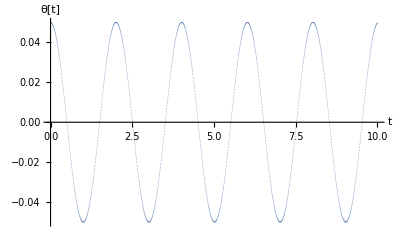

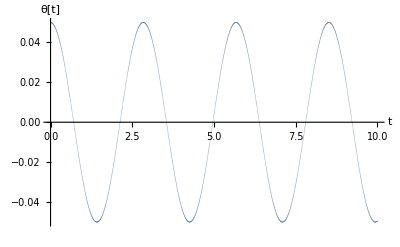

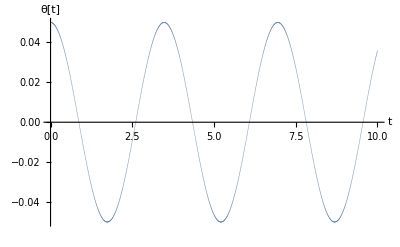

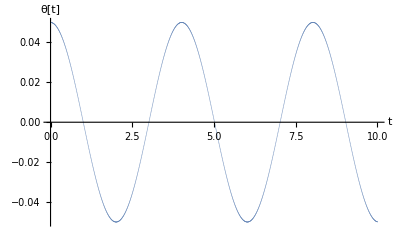

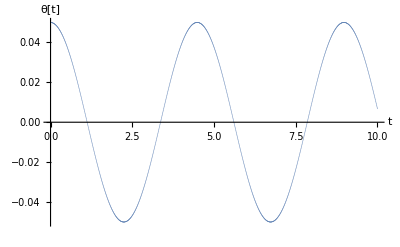

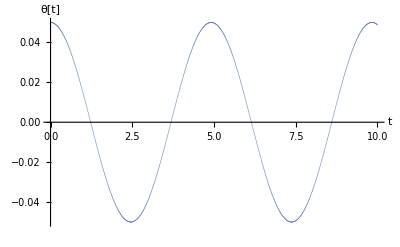

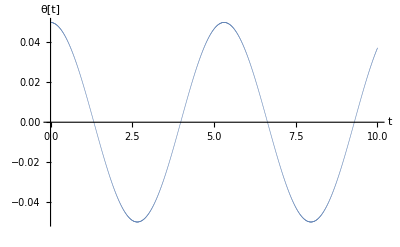

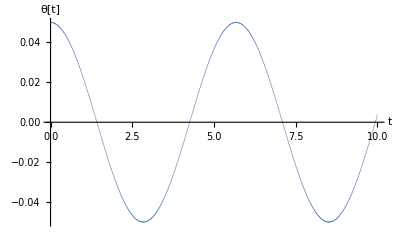

Length(m) | Period(s)
1 | 2.00709
2 | 2.83845
3 | 3.47638
4 | 4.01418
5 | 4.48799
6 | 4.91635
7 | 5.31026
8 | 5.67691
9 | 6.02127
10 | 6.34698
11 | 6.65676
12 | 6.95276
13 | 7.23667
14 | 7.50984
15 | 7.77343
16 | 8.02836
17 | 8.27544
18 | 8.51536
19 | 8.7487
20 | 8.97598
21 | 9.19764

Length(m) | Period(s)^2
1 | 4.02841
2 | 8.05682
3 | 12.0852
4 | 16.1136
5 | 20.142
6 | 24.1705
7 | 28.1989
8 | 32.2273
9 | 36.2557
10 | 40.2841
11 | 44.3125
12 | 48.3409
13 | 52.3693
14 | 56.3977
15 | 60.4261
16 | 64.4546
17 | 68.483
18 | 72.5114
19 | 76.5398
20 | 80.5682
21 | 84.5966

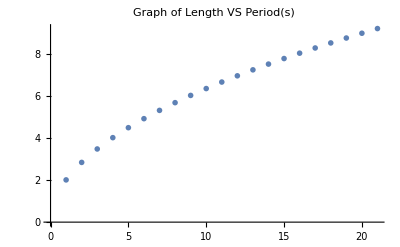

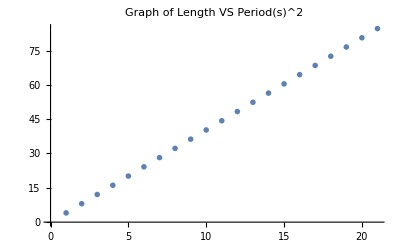

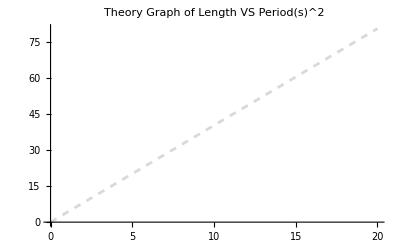

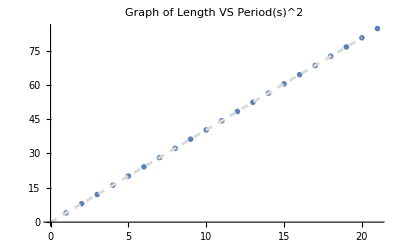

```mathematica
g=9.8;
L=2.0;
theta[0]=0.05;
ω[0]=0.0;
m=1.;
Δt=0.005;
TotalTime=10;
Steps=Round[TotalTime/Δt];
aa:=g/L;
e[0]=0;
plots={};
zdata={};
ydata={};
Ldata={};

For[
L=0,
L<=20,
L+=1;

Do[
F[n]=-aa*Sin[theta[n]];
ω[n+1]=ω[n]+F[n]*Δt;
theta[n+1]=theta[n]+ω[n+1]*Δt;
e[n+1]=1/2*m*(L*ω[n+1])^2+m*g*L*(1.-Cos[theta[n+1]]),{n,0,Steps}
];

x1data=Table[{n*Δt,theta[n]},{n,0,Steps}];
x1plot=ListPlot[x1data,AxesLabel->{"t","θ[t]"},PlotStyle->PointSize[0.001]];
Print[x1plot];

z=2Pi*Sqrt[L/g];
y=(2Pi*Sqrt[L/g])^2;

AppendTo[zdata,z];
AppendTo[ydata,y];
AppendTo[Ldata,L]
]

GridT=Grid[Join[{{"Length(m)","Period(s)"}},Transpose[{Ldata,zdata}]],Frame->All,Alignment->{Center,Center},Background->{{LightGray,None},{LightGray,None}}]

GridT2=Grid[Join[{{"Length(m)","Period(s)^2"}},Transpose[{Ldata,ydata}]],Frame->All,Alignment->{Center,Center},Background->{{LightGray,None},{LightGray,None}}]

T=ListPlot[Transpose[{Ldata,zdata}],PlotStyle->PointSize[.01],FrameLabel->{"Length(m)","Length(s)"},PlotLabel->"Graph of Length VS Period(s)"]
T2= ListPlot[Transpose[{Ldata,ydata}],PlotStyle->PointSize[.01],FrameLabel->{"Length(m)","Length(s)^2"},PlotLabel->"Graph of Length VS Period(s)^2"]

Theory =Plot[(4*Pi^2/g)*x,{x,0,20},PlotStyle->{Dashed,LightGray},FrameLabel->{"Length(m)","Length(s)^2"},PlotLabel->"Theory Graph of Length VS Period(s)^2"]

Show[T2,Theory]
```